# Integral Transforms

Integral transforms are operations that map a function of a real (or a complex) variable to another function of a real or a complex variable.

## Exploring the Integral Transforms

### Fourier Transform

This is probably the most well-known of all the integral transforms. The Fourier transform maps a real valued function f(t) to a complex valued function F(ω), where both t and ω are real variables.

Fourier transform of the unit pulse shown in the figure below

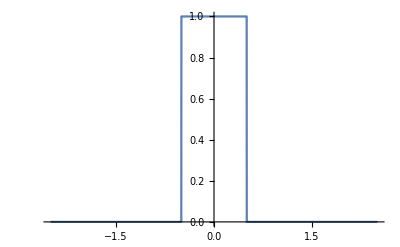

```mathematica
Plot[WaveletPhi[HaarWavelet[], t + 0.5], {t, -2.5, 2.5 }, Exclusions -> None]
```

```mathematica
ftUnitPulse = 1/Sqrt[2 π] Integrate[ WaveletPhi[HaarWavelet[], t + 0.5] Exp[-ⅈ ω t], {t, -Infinity, Infinity}]
```

(0.797885 Sin[0.5 ω])/ω

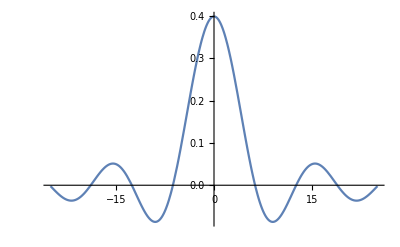

```mathematica
Plot[ftUnitPulse,{ω, -25, 25}]
```

Fourier transform of a delayed unit pulse

```mathematica
ftUnitPulseDelayed = 1/Sqrt[2 π] Integrate[WaveletPhi[HaarWavelet[], t]Exp[-ⅈ ω t], {t, -Infinity, Infinity}]
```

(-ⅈ+ⅈ Cos[ω]+Sin[ω])/(√(2 π) ω)

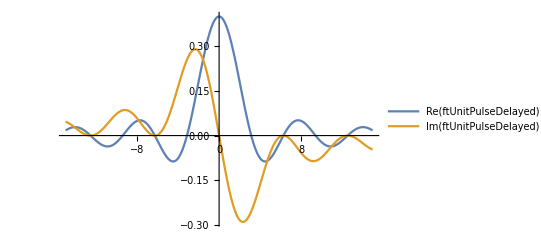

```mathematica
Plot[{Re[ftUnitPulseDelayed], Im[ftUnitPulseDelayed]}, {ω, -15, 15}, PlotLegends -> "Expressions"]
```

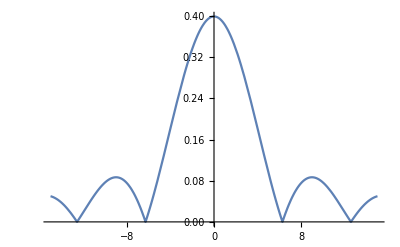

```mathematica
Plot[Abs[ftUnitPulseDelayed], {ω, -15, 15}]
```

Thus Fourier transforming a unit pulse gives sinc waves, however as we see that delaying the pulse gives rise to an imaginary component. If we think of t as time and ω as frequency then the plots indicate that introducing a delay in the time domain results in a phase shift in the frequency domain.

The unit pulse is a fairly simple function. Calculating the Fourier transforms of more complex functions can be quite computationally intensive. However Mathematica has built-in efficient Fourier transform capabilities.

Fourier transform of a Gaussian modulated by a sinusoidal function

```mathematica
ftGaussCos = FourierTransform[Cos[3t]Exp[-t^2], t, ω]
```

Cosh[1/4 (-3+ω)^2]/(2 √2)+Cosh[1/4 (3+ω)^2]/(2 √2)-Sinh[1/4 (-3+ω)^2]/(2 √2)-Sinh[1/4 (3+ω)^2]/(2 √2)

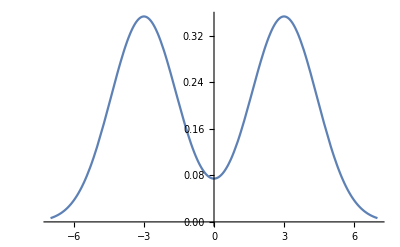

```mathematica
Plot[ftGaussCos, {ω, -7, 7}]
```

Fourier transform shows which frequencies are present in a function of time. For example the above plot shows that in our chosen Gaussian modulated by the sinusoidal function, ω = 3Hz is the dominant frequency.

### Laplace Transform

Like Fourier transform, Laplace transform maps a real valued function f(t) to a complex valued function F(s). The difference however lies in the fact that unlike ω in the Fourier transform, s itself is a complex variable. So we can think of Laplace transforms as a way of selecting the complex frequencies present in the time domain function f(t).

Laplace transform of sin(α t)

```mathematica
ltSin = Integrate[Exp[-s t] Sin[α t], {t, 0, Infinity}]
```

ConditionalExpression[α/(s^2+α^2),Abs[Im[α]]<Re[s]]

Let us try to visualize what this function of a complex variable looks like. For clarity we will take α to be real, in fact we will just put α = 1.

```mathematica
ltSin = Simplify[ltSin /. {α -> 1, s -> x + ⅈ y}, Assumptions-> {x, y} ∈ Reals]
```

ConditionalExpression[1/(1+(x+ⅈ y)^2),x>0]

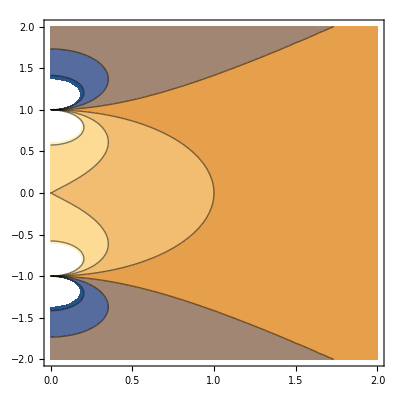
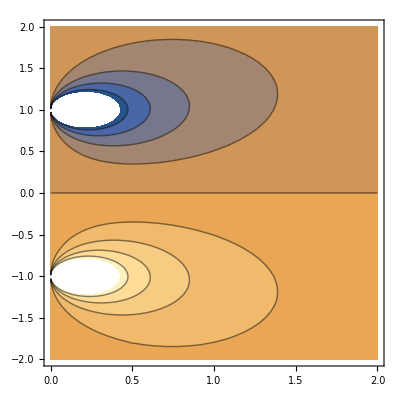

```mathematica
{ContourPlot[Re[ltSin ],{x,0,2}, {y,-2,2}], ContourPlot[Im[ltSin ],{x,0,2},{y,-2,2}]}
```

```mathematica
Plot3D[Abs[ltSin],{x,0,2.5},{y,-2.5,2.5}, BoxRatios->{1,1,1}]
```

-Graphics3D-

Mathematica has built-in functions that calculate Laplace transforms.

Laplace transform for cos(ω t)

```mathematica
ltCos = LaplaceTransform[Cos[ω t],t,s]
```

s/(s^2+ω^2)

```mathematica
ltCos = Simplify[ltCos /. {ω -> 1, s -> (x + ⅈ y)}, Assumptions-> {x, y} ∈ Reals]
```

(x+ⅈ y)/(1+(x+ⅈ y)^2)

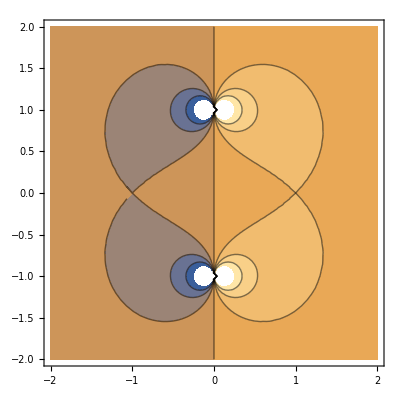
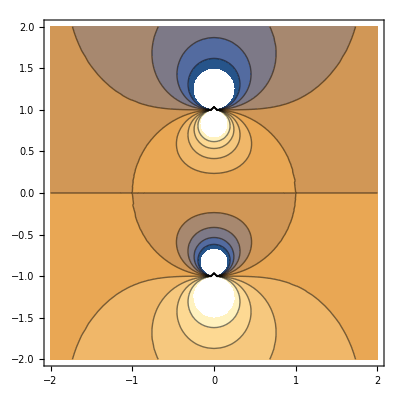

```mathematica
{ContourPlot[Re[ltCos ],{x,-2,2}, {y,-2,2}], ContourPlot[Im[ltCos ],{x,-2,2},{y,-2,2}]}
```

```mathematica
Plot3D[Abs[ltCos],{x,-2.5,2.5},{y,-2.5,2.5}, BoxRatios->{1,1,1}]
```

-Graphics3D-

Laplace transform of an exponential modulate by a sinusoidal

```mathematica
ltExpSin = LaplaceTransform[Exp[α t]Sin[β t], t, s]
```

β/((s-α)^2+β^2)

```mathematica
ltExpSin = Simplify[ltExpSin /. {α -> 1, β -> 1, s -> x + ⅈ y}, Assumptions-> {x, y} ∈ Reals]
```

1/(1+(-1+x+ⅈ y)^2)

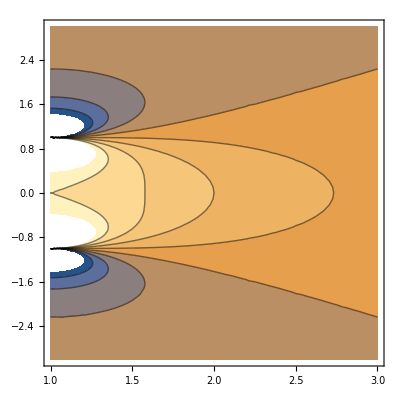
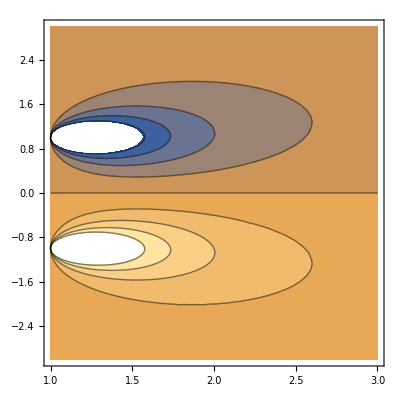

```mathematica
{ContourPlot[Re[ltExpSin], {x, 1, 3}, {y, -3, 3}], ContourPlot[Im[ltExpSin], {x, 1, 3}, {y, -3, 3}]}
```

```mathematica
Plot3D[Abs[ltExpSin], {x, 1, 3}, {y, -3, 3}, BoxRatios->{1, 1, 1}]
```

-Graphics3D-

### Mellin Transform

The Mellin Transform is closely related to the Laplace transform, it too maps a real valued function f(t) of a real variable t to a complex valued function F(s) of a complex variable s.

Mellin transform of a Gaussian

```mathematica
mtGauss = Integrate[Exp[-t^2] t^(s - 1), {t, 0, Infinity}]
```

ConditionalExpression[1/2 Gamma[s/2],Re[s]>0]

Visualizing the transform

```mathematica
mtGauss = Simplify[mtGauss /. {s -> x + ⅈ y}, {x, y} ∈ Reals]
```

ConditionalExpression[1/2 Gamma[1/2 (x+ⅈ y)],x>0]

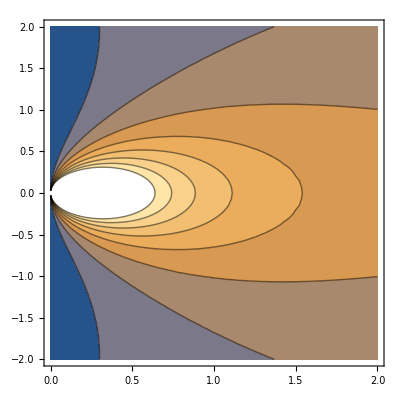
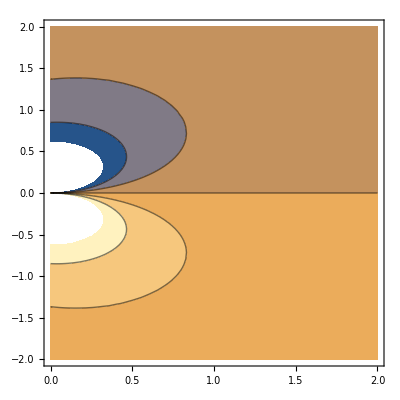

```mathematica
{ContourPlot[Re[mtGauss],{x, 0, 2}, {y, -2, 2}], ContourPlot[Im[mtGauss], {x, 0, 2}, {y, -2, 2}]}
```

```mathematica
Plot3D[Abs[mtGauss], {x, 0, 2}, {y, -2, 2}, BoxRatios->{1, 1, 1}]
```

-Graphics3D-

Mellin transform of a Ramp function using MellinTransform

```mathematica
mtRamp = MellinTransform[Ramp[t], t, s]
```

DiracDelta[1+s]

### Convolution

This is a bit different from the other three, yet closely related to them. Convolution is an integral transformation that takes in two functions of a real (or a complex) variable and returns a third function of another variable (of the same type as the other variable).

Convolution of the unit pulse and the inverse ramp functions plotted below.

```mathematica
unitPulse[t_] := WaveletPhi[HaarWavelet[], t]; invRamp[t_] := Piecewise[{{1-t, 0 < t ≤ 1}, {0, t < 0 && t > 1}}];
```

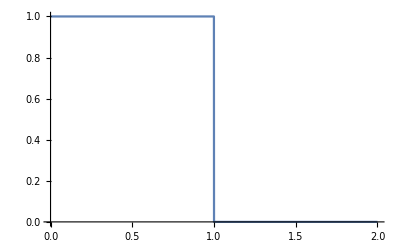
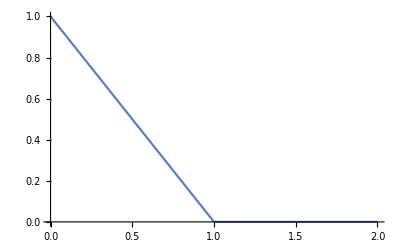

```mathematica
{Plot[unitPulse[t],{t, 0, 2}, Exclusions -> None], Plot[invRamp[t], {t, 0, 2}]}
```

```mathematica
conPulRamp[t_] := Integrate[unitPulse[τ] invRamp[t - τ], {τ, -Infinity, Infinity}]
```

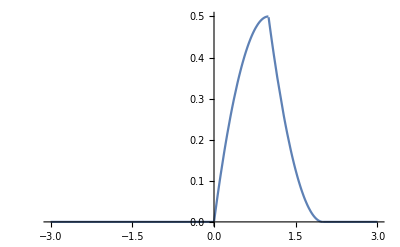

```mathematica
Plot[conPulRamp[t], {t, -3, 3}]
```

We can do the same using the built-in convolution capabilities.

Convolution of a Gaussian and a unit step function

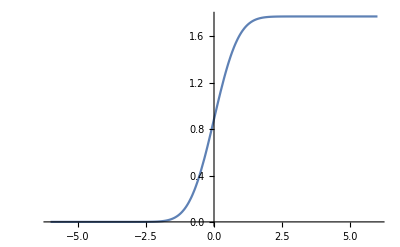

```mathematica
Plot[Convolve[Exp[-τ^2], UnitStep[τ], τ, t], {t, -6, 6}]
```

## Inverse transforms

These transformations would not be of much use if there were no transformations that were inverses of these. However as it turns out they do exist, at least in principle.

### Inverse Fourier Transform

The inverse Fourier transform takes us back from F(ω) to f(t).

Inverse Fourier transform of the sinc function. We should get a pulse as the answer.

```mathematica
invftSinc = InverseFourierTransform[Sqrt[2/π]Sinc[ω], ω, t]
```

1/2 (Sign[1-t]+Sign[1+t])

```mathematica
Plot[invftSinc, {t, -2, 2}, Exclusions -> None]
```

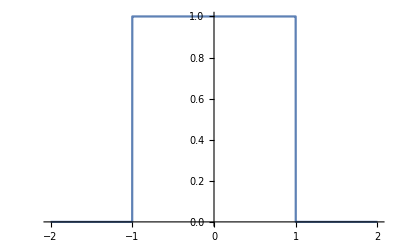

```mathematica
.12
```

It is indeed the unit pulse function.

### Inverse Laplace Transform

The inverse Laplace transform, given by the Bromwich integral, maps F(x), a function of a complex variable to f(t), a function of a real variable.

Let us try the inverse Laplace transformation on ω/(ω^2+ s^2). We expect the answer to be sin(ω t).

```mathematica
InverseLaplaceTransform[ω/(s^2 + ω^2), s, t]
```

Sin[t ω]

### Inverse Mellin Transform

The inverse Mellin transform is very similar in action to the inverse Laplace transform and plays an important role in number theory.

Let us what happens to the Dirac Delta when in undergoes the inverse Mellin transformation

```mathematica
InverseMellinTransform[DiracDelta[1 + s], s, t]
```

t

## Applications

These transforms along with their inverses have various applications. They are particularly helpful at solving differential equations and in signal processing. We have already seen that the Fourier transforms shows the dominant frequencies of time signals. Here are a few other examples of their applications.

### Solving differential equations via Laplace Transform

Let us solve the “radioactivity” equation A’(t) + λ A(t) = 0 for A, with the initial condition A(0) = 1. Here the ‘ denotes differentiation with respect to t and λ is a constant. We will first do it using the in-built Mathematica function DSolve and then see how we can use Laplace Transform to solve it.

```mathematica
DSolve[{A'[t] + λ A[t] == 0, A[0] == 1}, A[t], t]
```

{{A[t]→ⅇ^(-t λ)}}

And now we will do it using the Laplace Transform

```mathematica
LaplaceTransform[A'[t] + λ A[t],t,s]
```

-A[0]+s LaplaceTransform[A[t],t,s]+λ LaplaceTransform[A[t],t,s]

```mathematica
RSolveValue[-A[0]+s LaplaceTransform[A[t],t,s]+λ LaplaceTransform[A[t],t,s]== 0, LaplaceTransform[A[t],t,s], s]
```

A[0]/(s+λ)

```mathematica
InverseLaplaceTransform[A[0]/(s + λ), s, t] /. A[0] -> 1
```

ⅇ^(-t λ)

Voila! Both methods gave the same result. What we did in the Laplace Transformation method is that we converted a differential equation to an algebraic equation using the Laplace Transformation method, then we solved the algebraic equation and finally we used the Inverse Laplace Transformation to convert the solution to the desired form.

### Solving differential equations with Mellin Transform

Let us solve the equation r^2 F_(r r) + r F_r  + λ F= L with Mellin transform. Here the subscripts denote differentiation with respect to that variable and λ and L are constants.

```mathematica
MellinTransform[r^2 * D[F[r], {r, 2}] + r * D[F[r], r] + λ F[r], r, s]
```

-s MellinTransform[F[r],r,s]+s (1+s) MellinTransform[F[r],r,s]+λ MellinTransform[F[r],r,s]

```mathematica
RSolveValue[-s MellinTransform[F[r],r,s]+s (1+s) MellinTransform[F[r],r,s] +  λ MellinTransform[F[r], r, s] == L, MellinTransform[F[r],r,s], s]
```

L/(s^2+λ)

```mathematica
InverseMellinTransform[L/(s^2 + λ), s, r]
```

-(L Sin[√λ Log[r]])/(√λ)

```mathematica
Manipulate[Plot[-(L Sin[√λ Log[r]])/(√λ),{r,-8,8}],{L,-8,8},{λ,-2,2}]
```

### Convolution

As we mentioned earlier convolution is related to the other integral transformations. Let us see how.

```mathematica
ftUnitPulse = FourierTransform[WaveletPhi[HaarWavelet[], t], t, ω]
```

(ⅈ-ⅈ Cos[ω]+Sin[ω])/(√(2 π) ω)

```mathematica
ftInvRamp = FourierTransform[invRamp[t], t, ω]
```

(1+ⅈ ω-Cos[ω]-ⅈ Sin[ω])/(√(2 π) ω^2)

```mathematica
invftPulRamp = InverseFourierTransform[ftUnitPulse * ftInvRamp, ω, t]
```

-((-2+t) (-2 Sign[-2+t]+t Sign[-2+t]+2 Sign[-1+t]-2 t Sign[-1+t]+t Sign[t]))/(4 √(2 π))

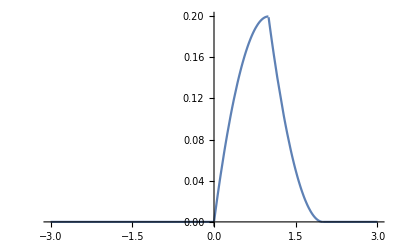

```mathematica
Plot[invftPulRamp, {t, -3, 3}]
```

See the connection? To find out the convolution of the unit pulse with the inverse ramp we first Fourier transformed both the functions, then multiplied them and finally inverse Fourier transformed the product. If we compare this plot to the one we obtained earlier using the direct method we will see that they match exactly. The idea here is that, depending on the limits of integration, the other three transformations map convolution in time domain to multiplication in frequency domain.

### Deconvolution

We had not mentioned earlier the inverse of convolution. But now equipped with our new found connection between convolution and the other transforms we can embark on the journey to discover deconvolution.

Let us first produce a convoluted function. We will convolve e^-twith the unit step function.

```mathematica
conSignal = Integrate[Exp[-τ] * UnitStep[t - τ], {τ, 0, Infinity}]
```

(1-Cosh[t]+Sinh[t]) UnitStep[t]

And now we will recover exp(-t) from this convoluted function

```mathematica
ltUnitStep = LaplaceTransform[UnitStep[t], t, ω]
```

1/ω

```mathematica
ltConSignal = LaplaceTransform[conSignal, t , ω]
```

1/ω+1/(-1+ω^2)-ω/(-1+ω^2)

```mathematica
InverseLaplaceTransform[ltConSignal / ltUnitStep, ω, t]
```

ⅇ^-t

What we did here is calculate the Laplace transforms of the convoluted function and the unit step function, divided the former by the latter and then calculated the inverse Laplace transform of the quotient to recover the exponential function.

It is this particular ability of deconvolution that makes these integral transforms very useful tools for signal processing. Usually we receive signals convoluted with a (known) carrier wave or we may receive signals distorted by an electrical filter or a spectrometer (effectively a convolution in the time domain) and we can use deconvolution to recover the original signal.

Further Explorations

Hankel Transform

Abel Transform

Z Transform

Wavelet Analysis

Authorship information

Soham Pal

2017/06/23

soham@iastate.edu